# Poizvodnja energije v Sloveniji

## Analiza proizvodnje energije v Sloveniji in njej sosednih držav (Austrija, Hrvaška, Madžarska)

## Pridobivanje podatkov

Podatke sem pridobila iz Our World In Data.

```mathematica
podatki = Import["/home/mikmik/Documents/codepato/ROM-2025/ROM-projekt/poraba-energije-po-drzavah.csv", "Dataset", "HeaderLines"->1]
```

Podatki zajemajo leta od 1990 do 2023 vključno.

## Analiza podatkov o proizvodnji energije v Sloveniji glede na vir

Analizirala in narisala bom graf števila proizvodenih TWh energije, glede na tip. Podatki bodo prikazani v pitni obliki.

```mathematica
LetniPrikazPoViru[drzava_, leto_] := PieChart[
Table[podatki[Select[#"Entity"==drzava&&#"Year"==leto&],{4,5,6,7,8,9,10,11,12}][1,i],{i,9}],
ImageSize->Large,
ChartStyle->"Pastel",
ChartLabels->{"Ostali","Biogorivo", "Sončna", "Veter", "Hidro", "Jedrska", "Plin","Premog","Olje"}
]
LetniPrikazPoViru["Slovenia", 2023]
```

-Graphics-

Narisala bom še graf proizvodenj čez leta.

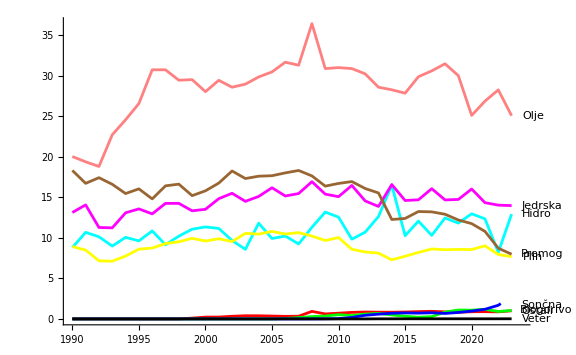

```mathematica
GrafPoViru[drzava_] := Show[Table[ListLinePlot[
Labeled[podatki[Select[#"Entity"==drzava&],{3,j+3}],{"Ostali","Biogorivo", "Sončna", "Veter", "Hidro", "Jedrska", "Plin","Premog","Olje"}[[j]]],
PlotStyle->{Red,Green,Blue,Black,Cyan,Magenta,Yellow,Brown,Pink}[[j]]
],{j,9}],
ImageSize->Large,
PlotRange->All
]

GrafPoViru["Slovenia"]
```

Iz zgornjih podatkov vidimo, da največ energije proizvedemo z oljem, medtem pa v zadnjih letih pada uporaba premoga.
Proizvod lahko primerjamo z Avstrijo.

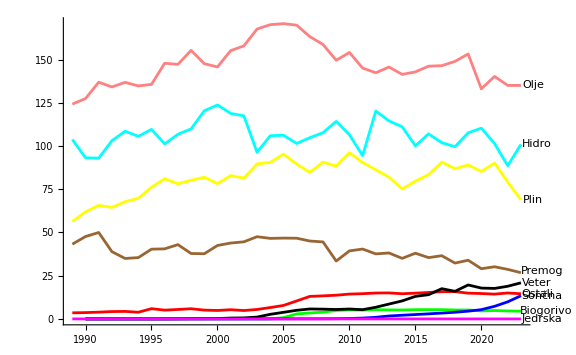

```mathematica
GrafPoViru["Austria"]
```

Tu vidimo, da čeprav obe državi večino energije pridobita iz olja, so avstrijci bolj razviti glede obnovljive energije.

### Delež obnovljive energije

Analizirala bom, kolikšen delež proizvedene energije je iz obnovljivih virov

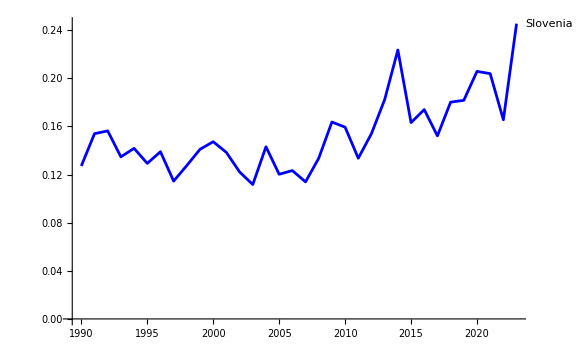

```mathematica
DelezObnovPoDrzavi[drzava_,color_] :=ListLinePlot[Labeled[Total[podatki[Select[#"Entity"==drzava&],Range[4,8]],{2}]/Total[podatki[Select[#"Entity"==drzava&],Range[4,12]],{2}],drzava],
PlotStyle->color,
DataRange->{1990,2023},
ImageSize->Large
] 
DelezObnovPoDrzavi["Slovenia",Blue]
```

Kot vidimo, počasi pridobivamo več energije iz obnovljivih virov, največ trenutno (2023), z 25% energije.
Sedaj pa še primerjava z sosednjimi državami.

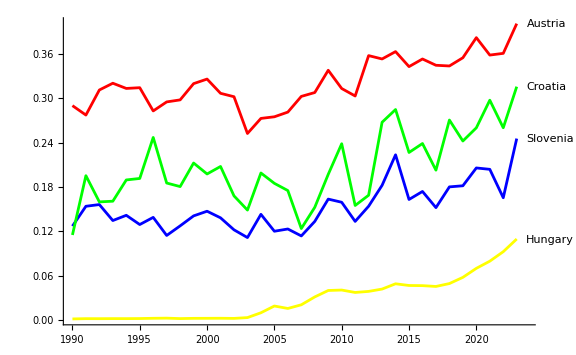

```mathematica
Show[{DelezObnovPoDrzavi["Slovenia",Blue],DelezObnovPoDrzavi["Austria",Red],DelezObnovPoDrzavi["Croatia",Green],DelezObnovPoDrzavi["Hungary",Yellow]},PlotRange->All]
```

## Analiza količine pridelane energije

Analizirala bom, koliko energije proizvedemo v Sloveniji in kasneje še primerjala z sosednjimi državami.

```mathematica
KolicinaPoDrzavi[drzava_,color_] :=ListLinePlot[Labeled[Total[podatki[Select[#"Entity"==drzava&],Range[4,12]],{2}],drzava],
PlotStyle->color,
DataRange->{1990,2023},
ImageSize->Large
] 
KolicinaPoDrzavi["Slovenia",Blue]
```

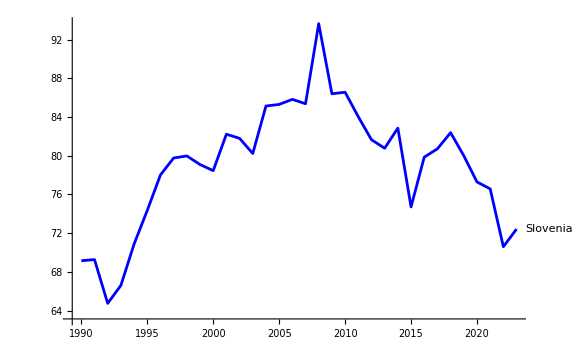

Sedaj pa še primerjajmo grafe sosednjih držav

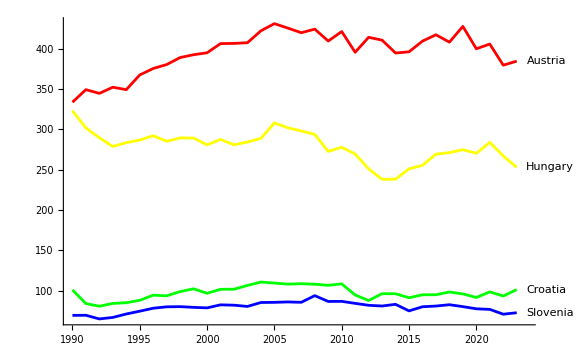

```mathematica
Show[{KolicinaPoDrzavi["Slovenia",Blue],KolicinaPoDrzavi["Austria",Red],KolicinaPoDrzavi["Croatia",Green],KolicinaPoDrzavi["Hungary",Yellow]},PlotRange->All]
```

Kot vidimo, Austrija in Madžarska proizvedeta veliko več energije, kar je smiselno, saj imata tudi večje število prebivalcev.